# Planar3D v3.4.0

```mathematica
ClearAll[folder,parameters,size,middle,cellLength,showAllBarriers,textPadding,ticks,barriers,concentration,fracture,opening,pressure,openingFilenames,openingAtCheckStep,numberOfCheckSteps,measuredTimes,totalTime];
```

## Построение сеточных графиков в 2D

Указываем путь до папки с входными данными

```mathematica
folder="C:\\Users\\Nikita\\Desktop\\Planar3D-master (2)\\Planar3D-master\\build\\Results\\";
If[!FileExistsQ[folder], Print[Style["Папка не существует!",{Red,FontSize->24}]]]
```

Считываем параметры расчёта

```mathematica
parameters=Import[folder<>"parameters.json","RawJSON"];
(*height=parameters["mesh"]["height"];
length=parameters["mesh"]["length"];
middleH = Floor[0.5*height]+1;
middleL=Floor[0.5*length]+1;*)
size=parameters["mesh"]["height"];
middle=Floor[0.5*size]+1;
cellLength=parameters["mesh"]["cell"]["length"];
```

Задаём параметры отображения

```mathematica
(*Если True, на графике будут выводиться границы слоёв,расположенных за пределами расчётной области*)
showAllBarriers=False;
textPadding=1;
```

Указываем риски по осям графика

```mathematica
(*ticksSetVertical={
{1,N[-cellLength*(middleH-0.5)]},
{1+Floor[height/4],N[-cellLength*(middleH-0.5)*0.5]},
{1+Floor[height/2],0},
{1+Floor[3height/4],N[cellLength*(middleH-0.5)*0.5]},
{height,N[cellLength*(middleH-0.5)]}
};
ticksSetHorizontal={
{1,N[-cellLength*(middleL-0.5)]},
{1+Floor[length/4],N[-cellLength*(middleL-0.5)*0.5]},
{1+Floor[length/2],0},
{1+Floor[3length/4],N[cellLength*(middleL-0.5)*0.5]},
{length,N[cellLength*(middleL-0.5)]}
};*)
(*ticks={{ticksSetHorizontal,None},{ticksSetVertical,None}};*)
createTicks=Function[{cellLength,middle,size},
ticksSet={
{1,N[-cellLength*(middle-0.5)]},
{1+Floor[size/4],N[-cellLength*(middle-0.5)*0.5]},
{1+Floor[size/2],0},
{1+Floor[3size/4],N[cellLength*(middle-0.5)*0.5]},
{size,N[cellLength*(middle-0.5)]}
};
{{ticksSet,None},{ticksSet,None}}
];
ticks=createTicks[cellLength,middle,size];
```

По рискам намечаем линии сетки

```mathematica
createLines=Function[{ticks},
lines={};
For[
i=1;AppendTo[lines,{}];leftTicks=ticks[[1]][[1]],
i≤ Length[leftTicks],
++i,
AppendTo[lines[[Length[lines]]],leftTicks[[i]][[1]]-0.5]
];
For[
i=1;AppendTo[lines,{}];rightTicks=ticks[[1]][[1]],
i≤ Length[rightTicks],
++i,
AppendTo[lines[[Length[lines]]],rightTicks[[i]][[1]]-0.5]
];
lines
];
lines=createLines[ticks];
```

Создаём массив линий–границ слоёв пласта

```mathematica
lineBarriers={};
nominalStress=0.;
For[
i=1; layers=parameters["layers"],
i<=Length[layers],
++i,
If[0>layers[ToString[i]]["y1"]*layers[ToString[i]]["y2"],nominalStress=layers[ToString[i]]["stress"]]
]
For[
i=1; layers=parameters["layers"],
i<=Length[layers],
++i,
barrierCoordinate=middle+Round[layers[ToString[i]]["y1"]/cellLength-0.5];
If[showAllBarriers||1≤barrierCoordinate && size≥barrierCoordinate,
AppendTo[lineBarriers,Line[{{1,barrierCoordinate},{size,barrierCoordinate}}]];
If[barrierCoordinate>middle ,
stress=layers[ToString[i-1]]["stress"],
stress=layers[ToString[i]]["stress"]
];
stress-=nominalStress;
stress/=10^6;
signum="";
If[stress > 0, signum="+"];
AppendTo[lineBarriers,Text[signum<>ToString[N[stress]]<>" МПа",{2+textPadding,textPadding+barrierCoordinate}]]
]
]
barriers=Graphics[lineBarriers];
```

Задаём функции для построения трещины и цветовую гамму

```mathematica
(*myRainbow=Function[x,Blend[{LightBlue,Green,LightGreen,White,Yellow,Orange,
RGBColor[0.6,0,0]},x]];*)
myRainbow=Function[x,Blend[{White,White,White,White,White,RGBColor[0.6,0.6,0.6],Yellow,Orange,RGBColor[0.6,0,0]},x]];
(*myRainbow=Function[x,If[0.5>x,White,ColorData["Rainbow",x]]];*)
myRainbow3D=Function[{x,y,z},ColorData["Rainbow",z]];
GlueMatrix=Function[{matrix},Transpose[Join[TakeList[Reverse[Transpose[matrix]],{Length[matrix[[1]]]-1}][[1]],Transpose[matrix]]]];
PlotMatrix= Function[{matrix,matrixName},
Show[
MatrixPlot[
GlueMatrix[matrix],PlotLabel->matrixName, FrameTicks->ticks,GridLines->lines,ColorFunction->myRainbow,PlotTheme->"Business",PlotLegends->Automatic,ImageSize->Large],
barriers]
];
```

Задаём функцию для построения графика характеристики трещины

```mathematica
plotCharacteristic=Function[{index,valueName},ListLinePlot[Table[{fracture[[i]][[1]],fracture[[i]][[index]]},{i,2,Length[fracture],1}],PlotRange->All,AxesLabel->{"Время, мин",valueName}]];
```

Задаём функцию для построения контура фронта трещины по граничным элементам

```mathematica
plotCircles=Function[{distances},
step=16;
margin=1;
color=Orange;
Graphics[
{color,Table[
Circle[
{i*step, -j*step},4*distances[[j]][[i]]
]
,{i,margin,Length[distances[[1]]]-margin + 1,1},{j,margin,Length[distances]-margin + 1,1}]},
ImageSize->Large
]
];
```

Задаём функцию для построения карты слоёв

```mathematica
plotLayersMap=Function[stressLine={};
plainModulusLine={};
carterLine={};
minY=100000;
maxY=-100000;
layers=parameters["layers"];
For[
i=0,
i< Length[layers],
++i,
y1=layers[ToString[i]]["y1"];
y2=layers[ToString[i]]["y2"];
plainModulus=N[layers[ToString[i]]["Young's modulus"]*10^-9/(1-Power[layers[ToString[i]]["Poisson's ratio"],2])];
AppendTo[stressLine,{N[layers[ToString[i]]["stress"]*10^-6],y1}];
AppendTo[stressLine,{N[layers[ToString[i]]["stress"]*10^-6],y2}];
AppendTo[plainModulusLine,{plainModulus,y1}];
AppendTo[plainModulusLine,{plainModulus,y2}];
AppendTo[carterLine,{N[layers[ToString[i]]["Carter's coefficient"]*10^6],y1}];
AppendTo[carterLine,{N[layers[ToString[i]]["Carter's coefficient"]*10^6],y2}];
minY=Min[{y1,y2,minY}];
maxY=Max[{y1,y2,maxY}];
];
minY=Max[{-0.5*cellLength*size,minY}];
maxY=Min[{-minY,maxY}];
plotStyles={{Red,Dotted},{Green,Dashed},{Purple,Dotted}};
plotLegend=Placed[LineLegend[{"Напряжения","Плоский модуль Юнга","Коэффициент Картера"},LegendLabel->"Карта слоёв", LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5],Right];
commonPlotParameters={ImageSize->{Tiny,Medium},AspectRatio->Full,AxesStyle->Transparent,PlotRange->{All,{minY,maxY}},Frame->{False,True,False,False}};
stressLinePlot=ListLinePlot[{stressLine,{None},{None}},PlotStyle->plotStyles,PlotLegends->plotLegend,commonPlotParameters];
plainModulusLinePlot=ListLinePlot[plainModulusLine,PlotStyle->plotStyles[[2]],commonPlotParameters];
carterLinePlot=ListLinePlot[carterLine,PlotStyle->plotStyles[[3]],commonPlotParameters];
Overlay[{stressLinePlot,plainModulusLinePlot,carterLinePlot}]];
```

Построение удвоенного графика

```mathematica
PlotDoubleMatrix= Function[{matrix,matrixName},
doubleTicks=createTicks[0.5*cellLength,2*(middle-1)+1,2*(size-1)+1];
doubleLines=createLines[doubleTicks];
Show[
MatrixPlot[
GlueMatrix[matrix],PlotLabel->matrixName, FrameTicks->doubleTicks,GridLines->doubleLines,ColorFunction->myRainbow,PlotTheme->"Business",PlotLegends->Automatic,ImageSize->Large]
]
];
```

Загружаем данные для построения

```mathematica
concentration=Import[folder<>"concentration_m.txt", "Table"];
fracture=Import[folder<>"fracture_m.txt", "Table"];
opening=Import[folder<>"opening_m.txt", "Table"];
pressure=Import[folder<>"pressure_m.txt", "Table"];
```

```mathematica
openingFilenames=FileNames["*_m.txt",folder<>"Opening/"];(*
If[1 <Length[openingFilenames],openingFilenames=SortBy[openingFilenames,ToExpression[StringSplit[#,{"=","_"}][[2]]&]]];*)
openingAtCheckStep=Function[t,Import[openingFilenames[[t]], "Table"]];
numberOfCheckSteps=Length[openingFilenames];
```

Выводим время последнего запуска

```mathematica
If[!FileExistsQ[folder], Print[Style["Папка не существует!",{Red,FontSize->24}]]]
Print[Style["Время последнего запуска:" Style[DateString[],Orange],{FontSize->24}]]
```

Время последнего запуска: Wed 6 Mar 2019 17:02:09

Строим графики

Длина, высота, раскрытие в источнике {м,м,мм}:
		 {134.345,47.0266,4.67128}

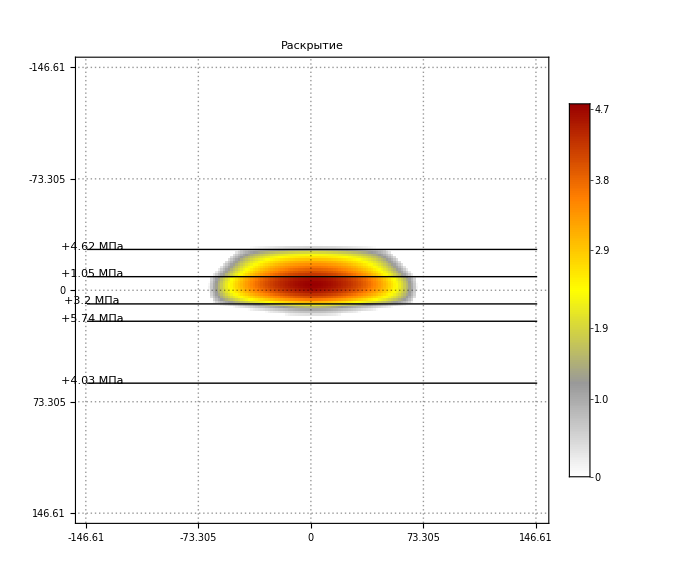

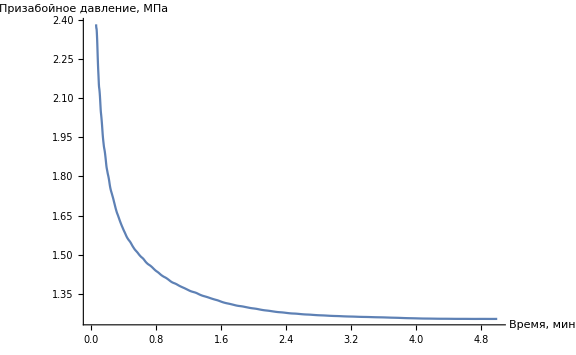

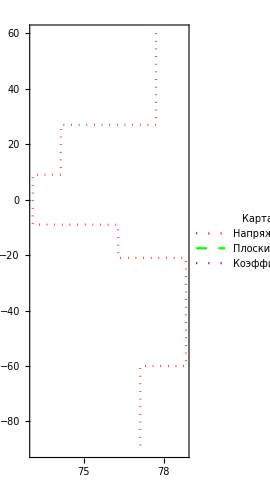
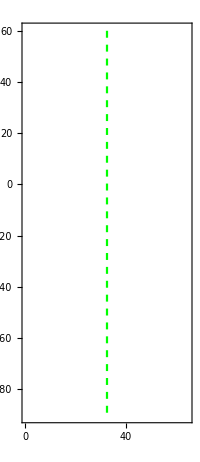
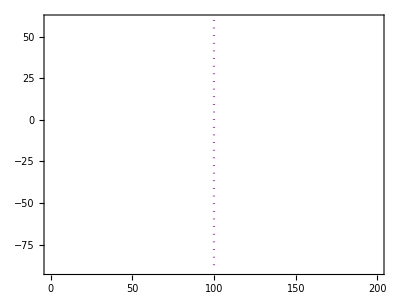

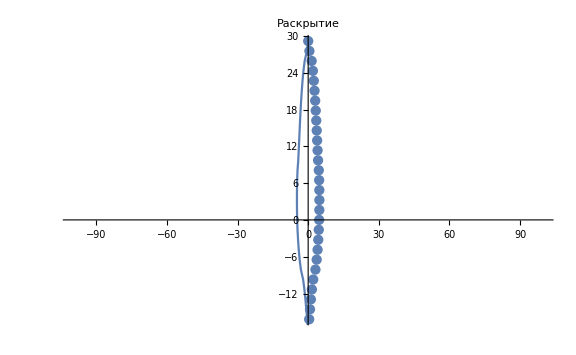

Null

```mathematica
Print[Style["Длина, высота, раскрытие в источнике {м,м,мм}:\n\t\t" Style[{fracture[[Length[fracture]]][[4]],fracture[[Length[fracture]]][[5]],fracture[[Length[fracture]]][[2]]},Orange],{FontSize->24}]]
PlotMatrix[opening, "Раскрытие"]
plotCharacteristic[3,"Призабойное давление, МПа"]
If[0<Max[concentration],PlotMatrix[concentration, "Концентрация проппанта"]]
plotLayersMap[]
Show[{
ListPlot[
Table[If[opening[[i]][[1]]>0,{opening[[i]][[1]],(middle-i)*cellLength}],{i,1,Length[opening],1}],
PlotRange->{{-100,100},All},PlotLabel->"Раскрытие"
],
ListLinePlot[
Table[If[opening[[i]][[1]]>=0,{-opening[[i]][[1]],(middle-i)*cellLength}],{i,1,Length[opening],1}],
PlotRange->All
]
}]
If[FileExistsQ[folder<>"times_v.txt"],
Print[Style["Замеры времени",{FontSize->24}]];
measuredTimes=Flatten[Import[folder<>"times_v.txt", "Table"]];
totalTime=measuredTimes[[Length[measuredTimes]]];
For[i=1,i<Length[measuredTimes],++i,measuredTimes[[i]]/=0.01*totalTime];
Labeled[
Grid[
Transpose[
{
{
"Расчёт давления",
"Прирост раскрытия\n(и концентрации)",
Style["Пересчёт расстояний\nдо фронта",TextAlignment->Center],
"Интегрирование",
"Перестроение списков",
"Сохранение шага",
"Изменение закачки",
"Масштабирование"
},
Table[measuredTimes[[i]],{i,1,Length[measuredTimes]-1,1}]
}
],Frame->All,Spacings->{Automatic,Automatic}],
totalTime/1000000"секунд всего",Bottom
]
]
```

Создаём GIF-анимацию

```mathematica
iterationStep=1;
plotName="Раскрытие";
plotDataList=Table[openingAtCheckStep[i],{i,1,numberOfCheckSteps,iterationStep}];
plotList=Table[
PlotMatrix[plotDataList[[i]],plotName<>" на шаге проверки №"<>ToString[1+(i-1)*iterationStep]],
{i,1,Length[plotDataList],1}
];
Export[folder<>"/opening.gif",plotList]
```

Export::errelem: The Export element ImageList contains a malformed data structure and could not be exported to GIF format.

$Failed

Экспериментальная секция!

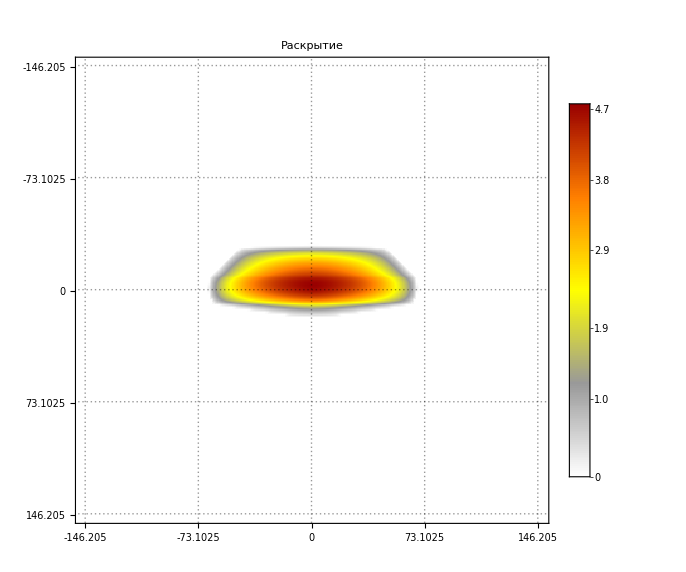

```mathematica
openingDouble={};
For[
i=1,
i<Length[opening],
++i,
AppendTo[openingDouble,{}];
For[
j=1,
j<Length[opening[[middle]]],
++j,
AppendTo[openingDouble[[2*(i-1)+1]],opening[[i]][[j]]];
AppendTo[openingDouble[[2*(i-1)+1]],0.5*(opening[[i]][[j]]+opening[[i]][[j+1]])]
];
AppendTo[openingDouble[[2*(i-1)+1]],opening[[i]][[Length[opening[[i]]]]]];

AppendTo[openingDouble,{}];
For[
j=1,
j<Length[opening[[middle]]],
++j,
AppendTo[openingDouble[[2*(i-1)+2]],0.5*(opening[[i]][[j]]+opening[[i+1]][[j]])];
AppendTo[openingDouble[[2*(i-1)+2]],0.5*(opening[[i]][[j]]+opening[[i+1]][[j+1]])]
];.
AppendTo[openingDouble[[2*(i-1)+2]],opening[[i]][[Length[opening[[i]]]]]];
]
PlotDoubleMatrix[openingDouble, "Раскрытие"]
```